```mathematica
SetDirectory[NotebookDirectory[]];
Needs["riemann`"]
```

### Utility functions

```mathematica
GeodesicEquations::usage="GeodesicEquations[chart,Γ,λ] returns the analytical expression of the geodesic equations in the coordinates 'chart' using the torsionlessconnexion 'Γ' and the affine parameter 'λ'.";
GeodesicEquations[coordinates_,christoffel_,λ_]:=
Module[{x=coordinates,n=Length@coordinates,Γ=christoffel,xλ,α,β},
xλ=Table[x[[i]]->x[[i]][λ],{i,1,n}];
Table[D[x[[i]][λ],{λ,2}]+∑_(α=1)^n ∑_(β=1)^n (Γ[[i,α,β]]/.xλ)D[x[[α]][λ],λ]D[x[[β]][λ],λ]==0,{i,1,n}]//Simplify
]
```

```mathematica
Embedding3D::usage="Embedding3D[map,chart,{{domx},{domy},...},curves,{domλ}] Returns a 3-dimensional plot repreenting the embedding of the submanifold defined by 'map' and with local coordinates 'chart' into the 3-dimensional euclidean space and draw 1-dimensional curves on the resulting surface. Domains '{{domx},{domy},...}' represent the boundaries of the surface in the directions of the coordinates in 'chart'. '{domλ}' is the domain of the affine parameter for the 'curves'. ";
Embedding3D[map_,coordinates_,listx_,curves_,listλ_,params___]:=Module[{xx=coordinates,n=Length@coordinates,p={params},xλ,list,λ=First@listλ,tab},
If[p=={},list={x,y,z}/.map,list={x,y,z}/.map/.First@p];
xλ=Table[xx⟦i⟧->xx⟦i⟧[λ],{i,1,n}];
tab=Table[list/.xλ/.curves⟦i⟧,{i,1,Length@curves}];
With[{temp=tab},
Show[ParametricPlot3D[list,Sequence@@listx//Evaluate,PlotStyle->Directive[Red,Opacity[0.3]]],ParametricPlot3D[temp,listλ,PlotStyle->Automatic],Axes->False,Boxed->False]
]
]
```

### Schwarzschild embedding

Define Manifold Μ with some coordinates and metric

```mathematica
chart={r,ϕ};
dim=Length[chart];
ds2 =dr^2/(1-rs/r)+r^2 dϕ^2;
g=Metric[ds2,chart];
g//MatrixForm
invg=Inverse[g];
```

(r/(r-rs) | 0
0 | r^2)

#### Initial value problem

```mathematica
params={rs->1};
```

```mathematica
Γ=Christoffel[g,chart];
geod=GeodesicEquations[chart,Γ,λ]
bc={r[0]==10,r'[0]==-2,ϕ[0]==0,ϕ'[0]==0.01};
line=NDSolve[Join[geod,bc]/.params,chart,{λ,0,10}];
```

{(rs r'[λ]^2)/(2 rs r[λ]-2 r[λ]^2)+(rs-r[λ]) ϕ'[λ]^2+r''[λ]==0,(2 r'[λ] ϕ'[λ])/r[λ]+ϕ''[λ]==0}

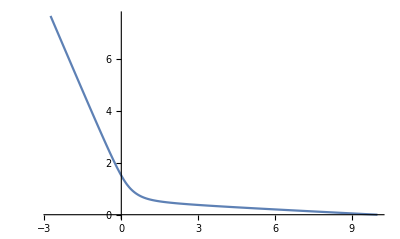

```mathematica
ParametricPlot[{r[λ]Cos[ϕ[λ]],r[λ]Sin[ϕ[λ]]}/.line,{λ,0,10}]
```

Flamm’s paraboloid embedding

```mathematica
mapΣ={x->r Cos[ϕ],y->r Sin[ϕ],z->2 √(r-1)};
Embedding3D[mapΣ,chart,{{r,0.5,10},{ϕ,0,2π}},line,{λ,0,10}]
```

-Graphics3D-

Here geodesics are simply paths of shortest length on the curved space, not space-time. Gravity is not taken into account.

### Schwarzschild space-time

Define Manifold Μ with some coordinates and metric

```mathematica
chart={t,r,θ,ϕ};
dim=Length[chart];
ds2 =-(1-rs/r)dt^2+dr^2/(1-rs/r)+r^2 dθ^2+r^2 Sin[θ]^2 dϕ^2;
g=Metric[ds2,chart];
g//MatrixForm
invg=Inverse[g];
```

(-1+rs/r | 0 | 0 | 0
0 | r/(r-rs) | 0 | 0
0 | 0 | r^2 | 0
0 | 0 | 0 | r^2 Sin[θ]^2)

```mathematica
dchart=Differential[chart];
```

```mathematica
Γ=Christoffel[g,chart];
geod=GeodesicEquations[chart,Γ,λ]
```

{t''[λ]==(rs r'[λ] t'[λ])/(rs r[λ]-r[λ]^2),(rs r'[λ]^2)/(2 rs r[λ]-2 r[λ]^2)+(rs (-rs+r[λ]) t'[λ]^2)/(2 r[λ]^3)+(rs-r[λ]) θ'[λ]^2+(rs-r[λ]) Sin[θ[λ]]^2 ϕ'[λ]^2+r''[λ]==0,Cos[θ[λ]] Sin[θ[λ]] ϕ'[λ]^2==(2 r'[λ] θ'[λ])/r[λ]+θ''[λ],(2 r'[λ] ϕ'[λ])/r[λ]+2 Cot[θ[λ]] θ'[λ] ϕ'[λ]+ϕ''[λ]==0}

#### Massive particle

```mathematica
params={rs->1};
```

Initial values: particle in the equatorial plane with a small azimutal velocity: (ϕ̇)_0= 1/50

```mathematica
ClearAll[t0,r0,dr0,θ0,dθ0,ϕ0,dϕ0];
t0=0;r0=10;dr0=0;θ0=π/2;dθ0=0;ϕ0=0;dϕ0=20/1000;
(* dt0 omitted intentionally *)
```

The above does not feature an expression for the initial derivative of the coordinate time. This is because the principle of equivalence sets an extra constraints on the coordinates of space-time. Indeed, at any point of space-time, and at the starting position in particular, the principle states that the laws of motion must be reducible to those of special relativity. This corresponds to the choice of a free-falling frame of reference. In the case of a massive particle, this amounts to demand that ds^2=-dλ^2 locally, where λ is here interpreted as the proper-time of the particle. The constraint is shown and solved for dt_0below.

```mathematica
ClearAll[dt0]
chart0=Table[chart⟦i⟧->ToExpression[StringJoin[ToString@chart⟦i⟧,"0"]],{i,1,dim}];
dchart0=Table[dchart⟦i⟧->ToExpression[StringJoin[ToString@dchart⟦i⟧,"0"]],{i,1,dim}];
ds2==-1/.Join[chart0,dchart0]
ass=rs>0&&r0>rs&&dt0>0;
Solve[ds2==-1&&ass/.Join[chart0,dchart0],dt0]//Simplify[#,Assumptions->ass]&;
dt0=First[dt0/.%];
```

1/25+dt0^2 (-1+rs/10)==-1

Numerical integration:

```mathematica
λend=1500;
range={λ,0,λend};
bc={t[0]==t0,t'[0]==dt0,r[0]==r0,r'[0]==dr0,θ[0]==θ0,θ'[0]==dθ0,ϕ[0]==ϕ0,ϕ'[0]==dϕ0};
line=NDSolve[Join[geod,bc]/.params,chart,range];
```

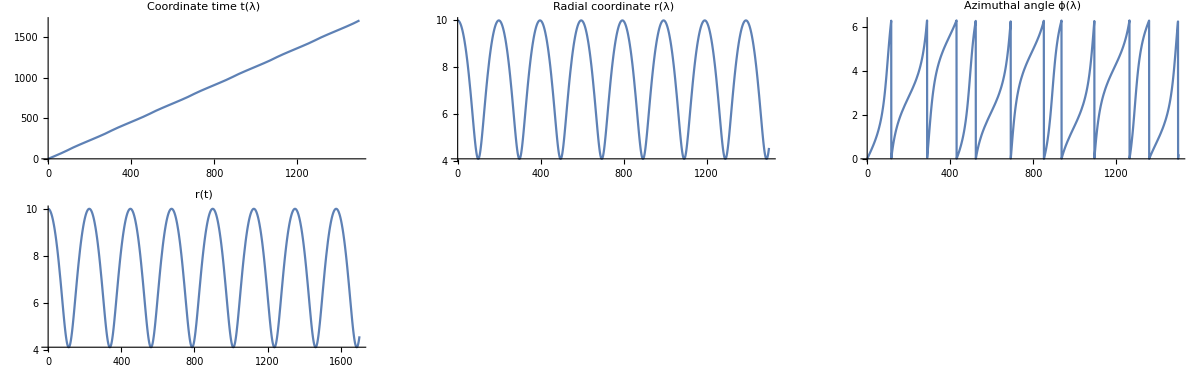

```mathematica
GraphicsGrid[{{Plot[t[λ]/.line,range,PlotLabel->"Coordinate time t(λ)"],Plot[r[λ]/.line,range,PlotLabel->"Radial coordinate r(λ)"],Plot[Mod[ϕ[λ],2π]/.line,range,PlotLabel->"Azimuthal angle ϕ(λ)"]},{ParametricPlot[{t[λ],r[λ]}/.line,{λ,0,λend},PlotLabel->"r(t)"]}},ImageSize->Full]
```

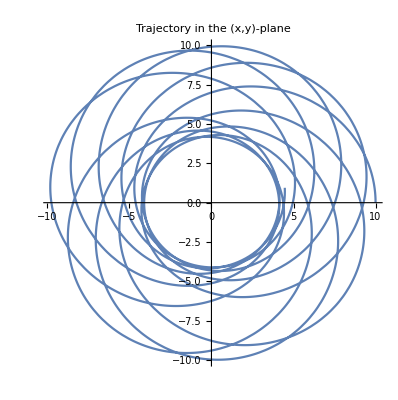

```mathematica
ParametricPlot[{r[λ]Cos[ϕ[λ]],r[λ]Sin[ϕ[λ]]}/.line,{λ,0,λend},PlotLabel->"Trajectory in the (x,y)-plane"]
```

Flamm’s paraboloid embedding

```mathematica
mapΣ={x->r Cos[ϕ],y->r Sin[ϕ],z->2 √(r-1)};
Embedding3D[mapΣ,chart,{{r,rs,r0}/.params,{ϕ,0,2π}},line,{λ,0,λend}]
```

-Graphics3D-

Geodesics are paths of shortest length in space-time.

#### Massless particle

```mathematica
params={rs->5/3};
```

The discussion on initial values presented above for the case of a massive particle needs to be modified in order to apply to the case where the particle is massless. 
Firstly, one must realise that the idea of proper-time is ill-defined in this case and one must therefore decide on another affine parameter. Perhaps the most natural choice consists in simply using the length of the curve λ = ℓ . Differentiating both side wrt λ and taking the square leads to (dℓ/dλ)^2=1 which constrains the spatial part of the metric. 
Secondly, the equivalence principle cannot be used here as a massless particle always travels at the speed of light and there exists therefore no referential in which it is at rest. The requirement that it travels at the speed of light, however, entails the constraint ds^2=0. We make use of both these constraints in order in what follows

```mathematica
ClearAll[t0,r0,dr0,θ0,dθ0,ϕ0,dϕ0];
t0=0;r0=5;dr0=-1/2;θ0=π/2;dθ0=0;ϕ0=0;dϕ0=(√(1-dr0^2))/r0;
(* dt0 omitted intentionally *)
```

```mathematica
ClearAll[dt0]
chart0=Table[chart⟦i⟧->ToExpression[StringJoin[ToString@chart⟦i⟧,"0"]],{i,1,dim}];
dchart0=Table[dchart⟦i⟧->ToExpression[StringJoin[ToString@dchart⟦i⟧,"0"]],{i,1,dim}];
ds2==0/.Join[chart0,dchart0]
ass=rs>0&&r0>rs&&dt0>0;
Solve[ds2==0&&ass/.Join[chart0,dchart0],dt0]//Simplify[#,Assumptions->ass]&;
dt0=First[dt0/.%];
```

3/4+1/(4 (1-rs/5))+dt0^2 (-1+rs/5)==0

Numerical integration:

```mathematica
λend=13;
range={λ,0,λend};
bc={t[0]==t0,t'[0]==dt0,r[0]==r0,r'[0]==dr0,θ[0]==θ0,θ'[0]==dθ0,ϕ[0]==ϕ0,ϕ'[0]==dϕ0};
line=NDSolve[Join[geod,bc]/.params,chart,range];
```

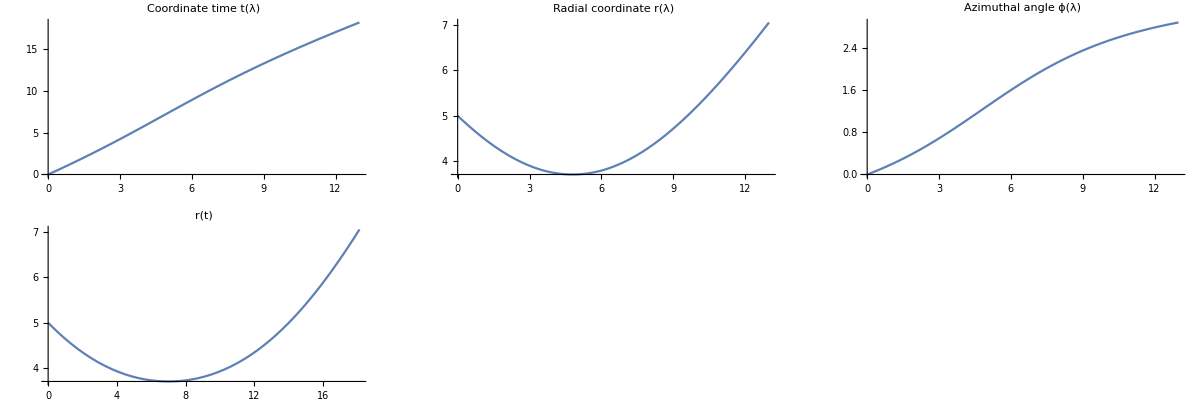

```mathematica
GraphicsGrid[{{Plot[t[λ]/.line,range,PlotLabel->"Coordinate time t(λ)"],Plot[r[λ]/.line,range,PlotLabel->"Radial coordinate r(λ)"],Plot[Mod[ϕ[λ],2π]/.line,range,PlotLabel->"Azimuthal angle ϕ(λ)"]},{ParametricPlot[{t[λ],r[λ]}/.line,{λ,0,λend},PlotLabel->"r(t)"]}},ImageSize->Full]
```

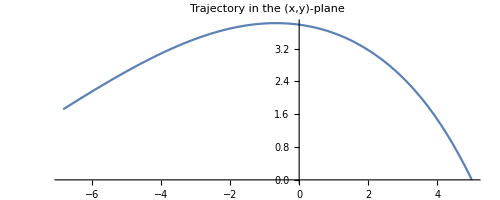

```mathematica
ParametricPlot[{r[λ]Cos[ϕ[λ]],r[λ]Sin[ϕ[λ]]}/.line,{λ,0,λend},PlotLabel->"Trajectory in the (x,y)-plane"]
```

The above clearly shows that the trajectories of massless particles is influenced by the curvature of space-time. It is perhaps the most stringent departure of general relativity from Newtonian physics that light rays are bent by gravitational fields.

As a comparison, the trajectory in a flat space-time is given below where we have simply set the Schwarzschild radius to zero.

```mathematica
params={rs->0};
ClearAll[dt0,t0,r0,dr0,θ0,dθ0,ϕ0,dϕ0];
t0=0;r0=5;dr0=-1/2;θ0=π/2;dθ0=0;ϕ0=0;dϕ0=(√(1-dr0^2))/r0;
λend=13;
range={λ,0,λend};
chart0=Table[chart⟦i⟧->ToExpression[StringJoin[ToString@chart⟦i⟧,"0"]],{i,1,dim}];
dchart0=Table[dchart⟦i⟧->ToExpression[StringJoin[ToString@dchart⟦i⟧,"0"]],{i,1,dim}];
ds2==0/.Join[chart0,dchart0]
ass=rs>0&&r0>rs&&dt0>0;
Solve[ds2==0&&ass/.Join[chart0,dchart0],dt0]//Simplify[#,Assumptions->ass]&;
dt0=First[dt0/.%];
bc={t[0]==t0,t'[0]==dt0,r[0]==r0,r'[0]==dr0,θ[0]==θ0,θ'[0]==dθ0,ϕ[0]==ϕ0,ϕ'[0]==dϕ0};
lineNewton=NDSolve[Join[geod,bc]/.params,chart,range];
```

3/4+1/(4 (1-rs/5))+dt0^2 (-1+rs/5)==0

Finally, let’s plot the two trajectories on the embedding diagram:

```mathematica
mapΣ={x->r Cos[ϕ],y->r Sin[ϕ],z->2 √(r-1)};
Embedding3D[mapΣ,chart,{{r,rs,1.5r0}/.params,{ϕ,0,2π}},Join[line,lineNewton],{λ,0,λend}]
```

-Graphics3D-